```mathematica
FinancialData["^SPX","Name"]
```

S&P 500 Index

```mathematica
data=FinancialData["^SPX","Close",All]["Values"]
```

QuantityArray[…]

```mathematica
Min@data
```

16.66

```mathematica
Grid@
Table[{f,f[data]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis}}]
```

Min | 16.66
Max | 3025.86
Max[#1]-Min[#1]& | 3009.2
Mean | 590.159
Quartiles | {86.2,168.445,1106.69}
Variance | 501441. None^2
Skewness | 1.3667
Kurtosis | 4.07652

```mathematica
Grid@
Table[{f,f[data]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
```

Min | 16.66
Max | 3025.86
Max[#1]-Min[#1]& | 3009.2
Mean | 590.159
Quartiles | {86.2,168.445,1106.69}
Variance | 501441. None^2
Skewness | 1.3667
Kurtosis | 4.07652
N[Entropy[#1]]& | 9.47031

```mathematica
RandomFunction[WienerProcess[.3,.5],{0,1,0.01}]
```

TemporalData[…]

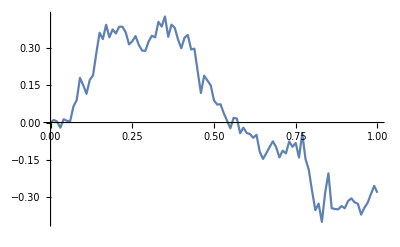

```mathematica
ListLinePlot[%7]
```

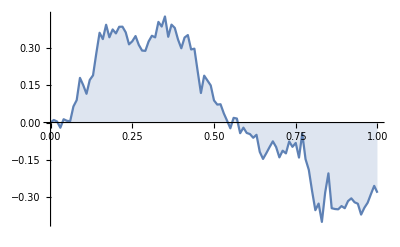

```mathematica
ListLinePlot[%7,Filling->Axis]
```

```mathematica
RandomFunction[WienerProcess[.3,.5],{0,1,0.01}]
```

```mathematica
RandomFunction[WienerProcess[.3,.5],{0,20,1}]
```

TemporalData[…]

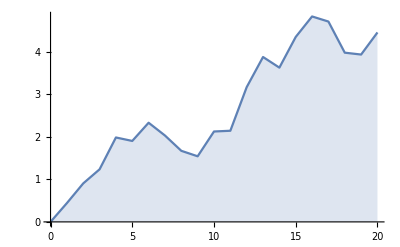

```mathematica
ListLinePlot[Out[10],Filling->Axis]
```

```mathematica
RandomFunction[WienerProcess[.3,.5],{0,20,.01}]
```

TemporalData[…]

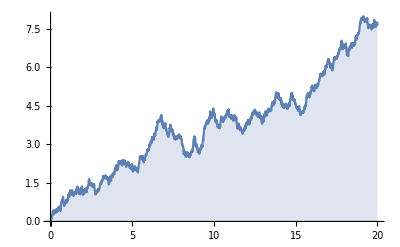

```mathematica
ListLinePlot[Out[12],Filling->Axis]
```

```mathematica
RandomFunction[WienerProcess[.3,.5],{0,20,.1}]
```

TemporalData[…]

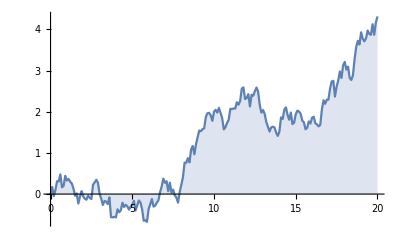

```mathematica
ListLinePlot[Out[14],Filling->Axis]
```

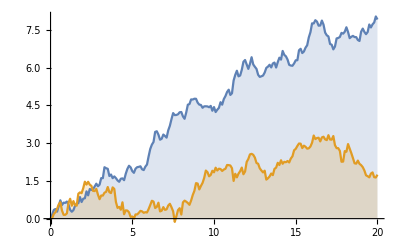

```mathematica
ListLinePlot[RandomFunction[WienerProcess[.3,.5],{0,20,.1},2],Filling->Axis]
```

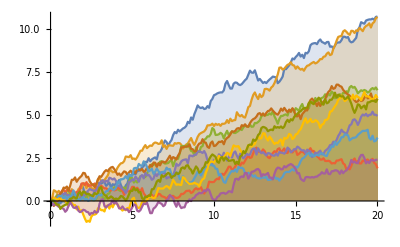

```mathematica
ListLinePlot[RandomFunction[WienerProcess[.3,.5],{0,20,.1},10],Filling->Axis]
```

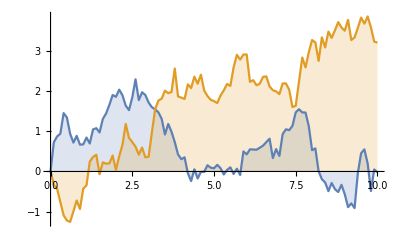

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
ListLinePlot[{a,b},Filling->Axis]
]
```

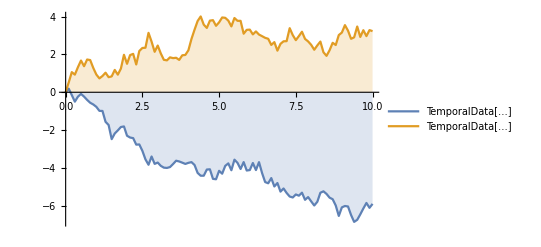

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
ListLinePlot[{a,b},Filling->Axis,PlotLegends->{a,b}]
]
```

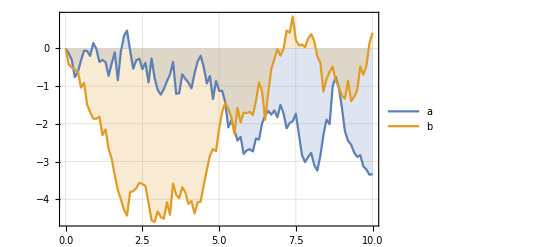

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
ListLinePlot[{a,b},Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Detailed"]
]
```

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
ListLinePlot[{a,b},Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing"]
]
```

-Graphics-

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]
]
```

-Graphics-

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]
]
```

-Graphics-

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
{
ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3],
Correlation[a["Values"],b["Values"]]
}
]
```

{-Graphics-,-0.75831}

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]}
}
]
```

Graph | -Graphics-
Correlation | 0.140844

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]}
}
]
```

Graph | -Graphics-
Correlation | -0.125889

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]}
}
]
```

Graph | -Graphics-
Correlation | -0.800826

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]}
}
]
```

Graph | -Graphics-
Correlation | 0.24009

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]}
}
]
```

Graph | -Graphics-
Correlation | -0.120071
Covariance | -0.0743684

```mathematica
Grid@
Table[{f,f[data]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
```

Min | 16.66
Max | 3025.86
Max[#1]-Min[#1]& | 3009.2
Mean | 590.159
Quartiles | {86.2,168.445,1106.69}
Variance | 501441. None^2
Skewness | 1.3667
Kurtosis | 4.07652
N[Entropy[#1]]& | 9.47031

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Grid@
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Grid@
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
}
]
```

Grid[{{Graph,-Graphics-},{Correlation,-0.66831},{Covariance,-0.465723},Min | -1.25926
Max | 1.71293
Max[#1]-Min[#1]& | 2.97219
Mean | 0.278312
Quartiles | {-0.122506,0.157021,0.73892}
Variance | 0.470621
Skewness | 0.196706
Kurtosis | 2.55958
N[Entropy[#1]]& | 4.61512,Min | -3.10609
Max | 0.728148
Max[#1]-Min[#1]& | 3.83424
Mean | -1.1307
Quartiles | {-1.92901,-1.06408,-0.288832}
Variance | 1.03188
Skewness | -0.133066
Kurtosis | 2.02413
N[Entropy[#1]]& | 4.61512}]

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Grid@
Join[{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
}
]]
```

Graph | -Graphics- |  |  |  |  |  |  | 
Correlation | -0.69184 |  |  |  |  |  |  | 
Covariance | -2.09558 |  |  |  |  |  |  | 
{Min,-2.10223} | {Max,2.92995} | {Max[#1]-Min[#1]&,5.03219} | {Mean,0.963754} | {Quartiles,{0.179311,1.23643,1.87603}} | {Variance,1.4276} | {Skewness,-0.706423} | {Kurtosis,2.73428} | {N[Entropy[#1]]&,4.61512}
{Min,-6.53891} | {Max,1.65054} | {Max[#1]-Min[#1]&,8.18945} | {Mean,-2.44421} | {Quartiles,{-5.12685,-2.14813,-0.189703}} | {Variance,6.42676} | {Skewness,-0.0632657} | {Kurtosis,1.52431} | {N[Entropy[#1]]&,4.61512}

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
}
]
```

{{Graph,-Graphics-},{Correlation,0.229214},{Covariance,0.15442},{{Min,-0.442964},{Max,2.97621},{Max[#1]-Min[#1]&,3.41917},{Mean,1.57609},{Quartiles,{0.92457,1.78744,2.25762}},{Variance,0.676779},{Skewness,-0.5981},{Kurtosis,2.33004},{N[Entropy[#1]]&,4.61512}},{{Min,-1.54148},{Max,2.0715},{Max[#1]-Min[#1]&,3.61298},{Mean,0.643096},{Quartiles,{0.176644,0.692377,1.14409}},{Variance,0.670622},{Skewness,-0.439306},{Kurtosis,2.95635},{N[Entropy[#1]]&,4.61512}}}

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
Join[{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
}
]
]
```

{{Graph,-Graphics-},{Correlation,0.261838},{Covariance,0.50921},{{Min,-2.04005},{Max,2.14392},{Max[#1]-Min[#1]&,4.18397},{Mean,0.376816},{Quartiles,{-0.752971,0.741858,1.34688}},{Variance,1.3735},{Skewness,-0.532925},{Kurtosis,1.97819},{N[Entropy[#1]]&,4.61512}},{{Min,-0.334705},{Max,6.24256},{Max[#1]-Min[#1]&,6.57726},{Mean,3.3956},{Quartiles,{2.56586,3.5067,4.78363}},{Variance,2.7536},{Skewness,-0.559002},{Kurtosis,2.59608},{N[Entropy[#1]]&,4.61512}}}

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},
{
{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
}
]
```

{{Graph,-Graphics-},{Correlation,-0.377064},{Covariance,-0.822698},{{Min,-6.11385},{Max,0.904264},{Max[#1]-Min[#1]&,7.01811},{Mean,-2.79872},{Quartiles,{-4.84586,-2.94265,-0.647815}},{Variance,4.83192},{Skewness,0.0424021},{Kurtosis,1.4267},{N[Entropy[#1]]&,4.61512}},{{Min,-2.98827},{Max,0.685635},{Max[#1]-Min[#1]&,3.67391},{Mean,-1.04389},{Quartiles,{-1.94233,-0.948613,-0.261743}},{Variance,0.985213},{Skewness,-0.0615016},{Kurtosis,1.78232},{N[Entropy[#1]]&,4.61512}}}

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},

Join[{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
]
]
```

{Graph,-Graphics-,Correlation,0.0579904,Covariance,0.131076,{Min,-2.34368},{Max,1.81329},{Max[#1]-Min[#1]&,4.15697},{Mean,-0.141573},{Quartiles,{-0.544632,-0.198891,0.252678}},{Variance,0.698033},{Skewness,-0.117725},{Kurtosis,3.5684},{N[Entropy[#1]]&,4.61512},{Min,-7.24999},{Max,1.88063},{Max[#1]-Min[#1]&,9.13062},{Mean,-1.71853},{Quartiles,{-3.78186,-1.66816,0.96884}},{Variance,7.31908},{Skewness,-0.308862},{Kurtosis,1.86673},{N[Entropy[#1]]&,4.61512}}

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},

Grid@
Join[{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
]
]
```

Grid[{Graph,-Graphics-,Correlation,0.0256519,Covariance,0.0181701,{Min,-1.16756},{Max,2.28196},{Max[#1]-Min[#1]&,3.44952},{Mean,1.00482},{Quartiles,{0.568833,1.02223,1.40924}},{Variance,0.373635},{Skewness,-0.418627},{Kurtosis,3.97288},{N[Entropy[#1]]&,4.61512},{Min,-1.45751},{Max,2.79211},{Max[#1]-Min[#1]&,4.24962},{Mean,0.687591},{Quartiles,{-0.249833,0.675392,1.56362}},{Variance,1.34285},{Skewness,0.118564},{Kurtosis,1.7418},{N[Entropy[#1]]&,4.61512}}]

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},

Grid@
Join[{{"Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"Correlation",Correlation[a["Values"],b["Values"]]},
{"Covariance",Covariance[a["Values"],b["Values"]]}},
Table[{f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
]
]
```

Graph | -Graphics-
Correlation | -0.323964
Covariance | -0.348793
Min | -2.88344
Max | 1.4589
Max[#1]-Min[#1]& | 4.34234
Mean | -0.942635
Quartiles | {-2.03927,-1.0198,0.176019}
Variance | 1.54491
Skewness | 0.202348
Kurtosis | 1.72133
N[Entropy[#1]]& | 4.61512
Min | -1.19386
Max | 2.3865
Max[#1]-Min[#1]& | 3.58036
Mean | 0.702552
Quartiles | {0.118919,0.720588,1.36087}
Variance | 0.750305
Skewness | -0.255847
Kurtosis | 2.49355
N[Entropy[#1]]& | 4.61512

```mathematica
+
```

```mathematica
With[{
a=RandomFunction[WienerProcess[],{0,10,.1}],
b=RandomFunction[WienerProcess[],{0,10,.1}]
},

Grid@
Join[{{"","Graph",ListLinePlot[{a,b},
Filling->Axis,PlotLegends->{"a","b"},PlotTheme->"Marketing",ImageSize->Full,AspectRatio->1/3]},
{"","Correlation",Correlation[a["Values"],b["Values"]]},
{"","Covariance",Covariance[a["Values"],b["Values"]]}},
Table[{"a",f,f[a["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}],
Table[{"b",f,f[b["Values"]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,N@Entropy@#&}}]
]
]
```

| Graph | -Graphics-
 | Correlation | 0.514164
 | Covariance | 1.41631
a | Min | -3.05025
a | Max | 2.61261
a | Max[#1]-Min[#1]& | 5.66287
a | Mean | -0.681627
a | Quartiles | {-2.11127,-1.0434,0.658511}
a | Variance | 2.48577
a | Skewness | 0.318083
a | Kurtosis | 1.85724
a | N[Entropy[#1]]& | 4.61512
b | Min | -6.45542
b | Max | 0.
b | Max[#1]-Min[#1]& | 6.45542
b | Mean | -2.38313
b | Quartiles | {-2.67515,-1.80396,-1.20426}
b | Variance | 3.05246
b | Skewness | -1.077
b | Kurtosis | 2.75624
b | N[Entropy[#1]]& | 4.61512